Crystal structure, Brillouin zone, and k paths

MagneticTB help home

Use a kagome antiferromagnet to draw the crystal structure, its magnetic moments, and the first Brillouin zone. The three in-plane moments are 120 degrees apart. After setting up this model, we obtain a k path and use it to plot the three bands.

Initialize the model

Choose magnetic space group 191.239, P6'/m'mm', with a = 1 and c = 4. One representative atom generates {1/2,0,0}, {0,1/2,0}, and {1/2,1/2,0}, in this order. Their moments in the lattice-vector basis are {1,0,0}, {0,1,0}, and {-1,-1,0}. In Cartesian coordinates, these are unit vectors 120 degrees apart and their sum is zero.

```mathematica
Needs["MagneticTB`"];
init[
  lattice -> {
    {a, 0, 0},
    {-a/2, Sqrt[3] a/2, 0},
    {0, 0, c}
  },
  lattpar -> {a -> 1, c -> 4},
  wyckoffposition -> {{{1/2, 0, 0}, {1, 0, 0}}},
  symminformation -> msgop[typeIII[{191, 239}]],
  basisFunctions -> {{{1, -1}/Sqrt[2]}},
  RepresentationMode -> "Induced"
];
```

Here {1,-1}/Sqrt[2] is one spinor at the representative site, not two independent basis states. Induced generates its counterparts at the other two sites. There is one state per site, giving a three-band Hamiltonian; keeping both spin states on every site would instead give six basis states.

Crystal structure

Draw 2 by 2 primitive cells. The picture contains twelve atoms and twelve red magnetic-moment arrows. MomentScale changes the arrow length. The gray lines mark cell edges, not hopping bonds. The default view uses an orthographic projection.

```mathematica
showCrystalStructure[
  "CellRange" -> {{0, 1}, {0, 1}, {0, 0}},
  "MomentScale" -> 0.3,
  ImageSize -> 400
]
```

-Graphics3D-

View 3 by 3 cells from above to see the repeating 120-degree magnetic pattern. There are twenty-seven atoms in this picture. CellRange changes how many cells are drawn, not the Hamiltonian:

```mathematica
Show[
  showCrystalStructure[
    "CellRange" -> {{0, 2}, {0, 2}, {0, 0}},
    "MomentScale" -> 0.3,
    ImageSize -> 400
  ],
  ViewPoint -> {0, 0, 3}, ViewVertical -> {0, 1, 0}
]
```

-Graphics3D-

Conventional path and first Brillouin zone

Use standardKPath to obtain the conventional path for this hexagonal lattice. The returned points are in reciprocal fractional coordinates. The function chooses a built-in path from the lattice metric; it does not calculate little-group irreducible representations.

```mathematica
kagomePath = standardKPath[]
```

{{{{0,0,0},{1/2,0,0}},{Γ,M}},{{{1/2,0,0},{1/3,1/3,0}},{M,K}},{{{1/3,1/3,0},{0,0,0}},{K,Γ}},{{{0,0,0},{0,0,1/2}},{Γ,A}},{{{0,0,1/2},{1/2,0,1/2}},{A,L}},{{{1/2,0,1/2},{1/3,1/3,1/2}},{L,H}},{{{1/3,1/3,1/2},{0,0,1/2}},{H,A}},{{{1/2,0,1/2},{1/2,0,0}},{L,M}},{{{1/3,1/3,0},{1/3,1/3,1/2}},{K,H}}}

For the in-plane bands, keep the first three segments, Gamma-M-K-Gamma at kz = 0. Use the same path in the Brillouin-zone and band plots:

```mathematica
planePath = Take[kagomePath, 3]
```

{{{{0,0,0},{1/2,0,0}},{Γ,M}},{{{1/2,0,0},{1/3,1/3,0}},{M,K}},{{{1/3,1/3,0},{0,0,0}},{K,Γ}}}

```mathematica
showBrillouinZone["KPath" -> planePath, ImageSize -> 400]
```

-Graphics3D-

The first Brillouin zone is a hexagonal prism, and the colored path is in its central plane. In this plot the fractional k points have been converted to Cartesian reciprocal coordinates using reciprocal vectors that include 2 Pi.

Hamiltonian and bands

Add symham[1] and symham[2] to keep onsite and nearest-neighbor terms. ComplexExpand and Simplify rewrite the paired exponentials as cosines for real k. The three rows and columns follow the site order given above:

```mathematica
kagomeHamiltonian = Simplify[ComplexExpand[symham[1] + symham[2]]];
kagomeHamiltonian // MatrixForm
```

(e1 | 2 t1 Cos[(kx+ky)/2] | 2 t1 Cos[ky/2]
2 t1 Cos[(kx+ky)/2] | e1 | -2 t1 Cos[kx/2]
2 t1 Cos[ky/2] | -2 t1 Cos[kx/2] | e1)

The common onsite energy is e1, and t1 is the nearest-neighbor hopping parameter. The relative minus sign in the (2,3) entry comes from the induced spinor basis used here. These terms contain no interlayer hopping, so the bands are independent of kz. This is an ideal kagome model, not a fit to a particular material.

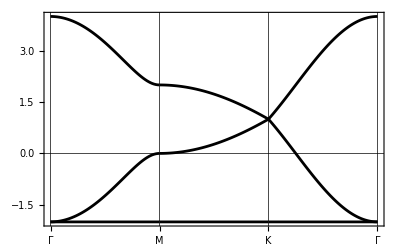

```mathematica
bandplot[
  planePath, 60, kagomeHamiltonian, {e1 -> 0, t1 -> -1},
  ImageSize -> 400, FontSize -> 16
]
```

Set e1 = 0 and t1 = -1 and plot the bands. The flat band has energy -2. The two dispersive bands meet at K at energy 1, while the flat band touches the lower dispersive band at Gamma. The energy unit is the magnitude of the hopping.

History